```mathematica
Integrate[Exp[-1/2(s-ν)^2/σ^2]Log2[ν/s], {s,ν-σ,ν+σ}, Assumptions->{σ<ν, ν>0}]
```

Integrate[(ⅇ^(-(s-ν)^2/(2 σ^2)) Log[ν/s])/Log[2],{s,ν-σ,ν+σ},Assumptions→{σ<ν,ν>0}]

## smth...

```mathematica
Integrate[1/(Sqrt[2 π σ^2])Exp[-1/2(s-ν)^2/σ^2](-(s-ν)/(ν Log[2])+(s-ν)^2/(2 ν^2 Log[2])),{s,ν-σ,ν+σ}]
```

(σ √(σ^2) (-√(2/(ⅇ π))+Erf[1/(√2)]))/(ν^2 Log[4])

```mathematica
Integrate[1/(Sqrt[2 π σ^2])Exp[-1/2(s-ν)^2/σ^2](-(s-ν)/(ν Log[2])+(s-ν)^2/(2 ν^2 Log[2])-(s-ν)^3/(3 (ν^3 Log[2]))),{s,-∞,∞}]
```

ConditionalExpression[(3 √(1/σ^2) σ^4)/(ν^2 √(σ^2) Log[64]),Re[σ^2]>0]

```mathematica
Integrate[Series[a,{tau,0,2}],{w,0,α}]
```

(sigma^2 α tau)/π+O[tau]^3

```mathematica
Series[- Log2[1-a/(a+v)], {a,0,5}]
```

a/(v Log[2])-a^2/(2 (v^2 Log[2]))+a^3/(3 v^3 Log[2])-a^4/(4 (v^4 Log[2]))+a^5/(5 v^5 Log[2])+O[a]^6

```mathematica
(Series[-1/2 Log2[1-a/(a+v)], {a,0,5}]*(2f))/.a->s/(2f)//FullSimplify
```

SeriesData::sdatv: First argument s/2\ f is not a valid variable.

(f s)/(v Log[2] 2 f)-(f (s/(2 f))^2)/(v^2 Log[4])+(f (s/(2 f))^3)/(v^3 Log[8])-(f (s/(2 f))^4)/(v^4 Log[16])+(f (s/(2 f))^5)/(v^5 Log[32])+O[s/(2 f)]^6

## small τ limit

```mathematica
a = 1/(2*π)*2*sigma^2*tau/(1+w^2*tau^2);
```

```mathematica
Integrate[a,{w,-∞,∞}]
```

ConditionalExpression[(sigma^2 tau)/(√(tau^2)),Im[tau^2]≠0||Re[tau^2]≥0]

```mathematica
Series[(2 sigma^2 ArcTan[tau α])/π,{tau,0,6}]
```

(2 sigma^2 α tau)/π-(2 (sigma^2 α^3) tau^3)/(3 π)+(2 sigma^2 α^5 tau^5)/(5 π)+O[tau]^7

```mathematica
Limit[(2 sigma^2 ArcTan[tau α])/π,α->∞]
```

(sigma^2 √(tau^2))/tau

```mathematica
Series[a,{tau,0,3}]
```

(sigma^2 tau)/π-(sigma^2 w^2 tau^3)/π+O[tau]^4

```mathematica
Integrate[Series[a, {tau,0,5}], {w,-α,α}]
```

(2 sigma^2 tau α (15-5 tau^2 α^2+3 tau^4 α^4))/(15 π)

```mathematica
Integrate[Series[-1/(2ν) Log2[1-a/(a+ν)], {tau,0,2}], {w,0,α}]/. α->π/(2 tau)
```

sigma^2/(4 ν^2 Log[2])-(sigma^4 tau)/(8 (π ν^3 Log[2]))+O[tau]^3

```mathematica
Limit[Integrate[Series[-1/(2ν) Log2[1-a/(a+ν)], {tau,0,2}], {w,-α,α}]/. α->π/(2 tau),tau->0]
```

sigma^2/(2 ν^2 Log[2])

```mathematica
Integrate[Series[-1/(2ν) Log2[1-a/(a+ν)], {tau,0,5}], {w,0,α}]/. {sigma-> σ Sqrt[π/(α*tau)]}//FullSimplify//Expand
```

σ^2/(2 ν^2 Log[2])-(tau^2 α^2 σ^2)/(6 ν^2 Log[2])+(tau^4 α^4 σ^2)/(10 ν^2 Log[2])-σ^4/(4 α ν^3 Log[2])+(tau^2 α σ^4)/(6 ν^3 Log[2])-(tau^2 σ^6)/(6 ν^4 Log[2])+σ^6/(6 α^2 ν^4 Log[2])-σ^8/(8 α^3 ν^5 Log[2])+σ^10/(10 α^4 ν^6 Log[2])

```mathematica
Integrate[-1/(2ν) Log2[1-a/(a+ν)], {w,-∞,∞}]//FullSimplify//Expand
```

ConditionalExpression[-π/(√(tau^2) ν Log[2])+(√π sigma^2 √((tau^2 ν)/(sigma^2 tau+π ν)))/(tau ν^2 Log[2])+(π^(3/2) √((tau^2 ν)/(sigma^2 tau+π ν)))/(tau^2 ν Log[2]),(√(-sigma^2 tau-π ν))/(tau √ν)∉Reals&&Re[tau]≠0&&Re[(√(sigma^2 tau+π ν))/(tau √ν)]≠0]

```mathematica
FullSimplify[-π/(√(tau^2) ν Log[2])+(√π sigma^2 √((tau^2 ν)/(sigma^2 tau+π ν)))/(tau ν^2 Log[2])+(π^(3/2) √((tau^2 ν)/(sigma^2 tau+π ν)))/(tau^2 ν Log[2]), tau>0 && ν>0 && sigma>0 &&sigma<ν]
```

(√π sigma^2 tau+π^(3/2) ν-π √(ν (sigma^2 tau+π ν)))/(tau √(ν^3 (sigma^2 tau+π ν)) Log[2])

```mathematica
Limit[-π/(√(tau^2) ν Log[2])+(√π sigma^2 √((tau^2 ν)/(sigma^2 tau+π ν)))/(tau ν^2 Log[2])+(π^(3/2) √((tau^2 ν)/(sigma^2 tau+π ν)))/(tau^2 ν Log[2]),tau->0]
```

sigma^2/(ν^2 Log[4])

```mathematica
TeXForm[(√π sigma^2 tau+π^(3/2) ν-π √(ν (sigma^2 tau+π ν)))/(tau √(ν^3 (sigma^2 tau+π ν)) Log[2])]
```

\frac{\pi ^{3/2} \nu -\pi  \sqrt{\nu  \left(\pi  \nu +\sigma ^2 \tau \right)}+\sqrt{\pi } \sigma ^2 \tau }{\tau  \log (2) \sqrt{\nu ^3 \left(\pi  \nu +\sigma ^2 \tau \right)}}

```mathematica
Integrate[a,{w,-∞,∞}]
```

ConditionalExpression[(sigma^2 tau)/(√(tau^2)),Im[tau^2]≠0||Re[tau^2]≥0]

```mathematica
Limit[-π/(√(tau^2) ν Log[2])+(√π sigma^2 √((tau^2 ν)/(sigma^2 tau+π ν)))/(tau ν^2 Log[2])+(π^(3/2) √((tau^2 ν)/(sigma^2 tau+π ν)))/(tau^2 ν Log[2]), tau->0]
```

sigma^2/(ν^2 Log[4])

```mathematica
Series[-f/ν*Log2[1-s/(2 f)/(ν+s/(2 f))], {f,0,2}]
```

((-Log[f]-Log[(2 ν)/s]) f)/(ν Log[2])+(2 f^2)/(s Log[2])+O[f]^3

```mathematica
Series[-1/(2 ν A)*Log2[1-s*A/(ν+s*A)], {A,0,2}]
```

s/(2 ν^2 Log[2])-(s^2 A)/(4 (ν^3 Log[2]))+(s^3 A^2)/(6 ν^4 Log[2])+O[A]^3

## attempt: hom. Poisson for signal entropy

```mathematica
Series[1/2 Log2[a+ν], {tau,0,2}]
```

Log[ν]/(2 Log[2])+(sigma^2 tau)/(2 π ν Log[2])-(sigma^4 tau^2)/(4 (π^2 ν^2 Log[2]))+O[tau]^3

```mathematica
Series[a+ν,{tau,0,2}]
```

ν+(sigma^2 tau)/π+O[tau]^3

```mathematica
b = 1/(2*π)*2*sigmaNu^2*tau/(1+w^2*tau^2)
```

(sigmaNu^2 tau)/(π (1+tau^2 w^2))

```mathematica
Integrate[Series[b,{tau,0,2}],{w,0,α}]
```

(sigmaNu^2 α tau)/π+O[tau]^3

α = π/τ

```mathematica
Integrate[Series[1/(2ν) Log2[b], {tau,0,2}], {w,0,α}]//FullSimplify//Expand
```

-(tau^2 α^3)/(ν Log[64])-(3 α Log[π])/(ν Log[64])+(3 α Log[tau])/(ν Log[64])+(3 α Log[ν^2])/(ν Log[64])

```mathematica
(x-ν)/(ν Log[2])+(x-ν)^2/(2 ν^2 Log[2])-(x-ν)^3/(6 (ν^3 Log[2]))+(x-ν)^4/(12 ν^4 Log[2])
```

```mathematica
higherM[n_]:= 1/2*Sum[(ν+k ν σ-ν)^n, {k,{-1,1}}]
```

```mathematica
higherM[1]//FullSimplify
```

0

```mathematica
higherM[8]//Expand
```

ν^8 σ^8

```mathematica
Solve[v^2==4*σ^2 μ λ/(μ+λ)^2 && μ+λ==1/τ, {μ, λ}]
```

{{μ→(σ^2 τ-√(-v^2 σ^2 τ^2+σ^4 τ^2))/(2 σ^2 τ^2),λ→(1+(√(σ^2 (-v^2+σ^2) τ^2))/(σ^2 τ))/(2 τ)},{μ→(σ^2 τ+√(-v^2 σ^2 τ^2+σ^4 τ^2))/(2 σ^2 τ^2),λ→(1-(√(σ^2 (-v^2+σ^2) τ^2))/(σ^2 τ))/(2 τ)}}

```mathematica
Limit[(σ^2 τ-√(-v^2 σ^2 τ^2+σ^4 τ^2))/(2 σ^2 τ^2), τ-> 0]
```

DirectedInfinity[σ^2-√(-v^2 σ^2+σ^4)]/σ^2

```mathematica
Solve[σ^2==4*σ^2 μ λ/(μ+λ)^2 && μ+λ==1/τ, {μ, λ}]/.{v->σ}//FullSimplify
```

{{μ→1/(2 τ),λ→1/(2 τ)}}

```mathematica
FourierTransform[Exp[-Abs[t]/τ],t , f]//FullSimplify
```

(√(2/π) τ)/(1+f^2 τ^2)

```mathematica
D[s Log2[s/ν], {s,4}]
```

2/(s^3 Log[2])

```mathematica
Series[Log2[1-x], {x,0,3}]
```

-x/Log[2]-x^2/(2 Log[2])-x^3/(3 Log[2])+O[x]^4

```mathematica
(1-x) Series[Log2[1-x], {x,0,3}]
```

-x/Log[2]+x^2/(2 Log[2])+x^3/(6 Log[2])+O[x]^4

## different distributions for r

```mathematica
tele[ν_, σ_]:= 1/2*Sum[(ν+k σ)/ν Log2[(ν+k σ)/ν], {k,{-1,1}}];
uni[ν_, σ_]:= Integrate[1/(2 Sqrt[3] σ) k/ν Log2[k/ν],{k, -Sqrt[3] σ+ν, Sqrt[3] σ+ν}];
OU[ν_, σ_]:= NIntegrate[PDF[NormalDistribution[ν, σ], k] k/ν Log2[k/ν],{k, 0, ∞}];
```

```mathematica
FullSimplify[uni[nu, sigma], Re[nu/sigma]>Sqrt[3]]
```

(-2 √3 nu sigma-(nu^2-2 √3 nu sigma+3 sigma^2) Log[1-(√3 sigma)/nu]+(nu^2+2 √3 nu sigma+3 sigma^2) Log[1+(√3 sigma)/nu])/(√3 nu sigma Log[16])

```mathematica
%//TeXForm
```

\frac{-\left(\nu ^2-2 \sqrt{3} \nu  \sigma +3 \sigma ^2\right) \log \left(1-\frac{\sqrt{3} \sigma }{\nu }\right)+\left(\nu ^2+2 \sqrt{3} \nu  \sigma +3 \sigma ^2\right) \log \left(\frac{\sqrt{3}
   \sigma }{\nu }+1\right)-2 \sqrt{3} \nu  \sigma }{\sqrt{3} \nu  \sigma  \log (16)}

```mathematica
FortranForm[%52]
```

(-2*Sqrt(3)*nu*sigma - (nu**2 - 2*Sqrt(3)*nu*sigma + 3*sigma**2)*Log(1 - (Sqrt(3)*sigma)/nu) + (nu**2 + 2*Sqrt(3)*nu*sigma + 3*sigma**2)*Log(1 + (Sqrt(3)*sigma)/nu))/(Sqrt(3)*nu*sigma*Log(16))

```mathematica
FullSimplify[tele[nu, sigma], Re[nu/sigma]>1]
```

((nu+sigma) Log[(nu+sigma)/nu]+(nu-sigma) Log[1-sigma/nu])/(nu Log[4])

#### does uni only dependen on σ/ν?

```mathematica
uni[ν, σ]/. σ-> k ν //FullSimplify
```

ConditionalExpression[(-2 √3 k+(-1+2 √3 k-3 k^2) Log[1-√3 k]+(1+2 √3 k+3 k^2) Log[1+√3 k])/(√3 k Log[16]),Re[1/k]>√3||√3+Re[1/k]<0||1/k∉Reals]

```mathematica
tele[ν, σ]/. σ-> k ν //FullSimplify
```

(-(-1+k) Log[1-k]+(1+k) Log[1+k])/Log[4]

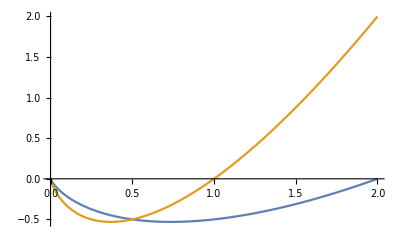

```mathematica
Plot[{(x Log2[x/2])/2,(x Log2[x]) },{x,0,2}]
```

```mathematica
Series[x/a Log2[x/a], {x,a,5}]
```

(x-a)/(a Log[2])+(x-a)^2/(2 a^2 Log[2])-(x-a)^3/(6 (a^3 Log[2]))+(x-a)^4/(12 a^4 Log[2])-(x-a)^5/(20 (a^5 Log[2]))+O[x-a]^6

```mathematica
OU[.1, .001]//N
```

3.32193

```mathematica
PDF[NormalDistribution[ν, σ]]
```

Exp[-1/2 ((#1-ν)/σ)^2]/(σ √(2 π))&

```mathematica
Integrate[1/(2 Sqrt[3] σ) (k-ν)^2,{k, -Sqrt[3] σ+ν, Sqrt[3] σ+ν}]//FullSimplify
```

σ^2

```mathematica
Series[tele[ν, σ], {σ, 0, 4}]
```

σ^2/(2 ν^2 Log[2])+σ^4/(12 ν^4 Log[2])+O[σ]^5

```mathematica
Series[uni[ν, σ], {σ, 0, 4}]
```

ConditionalExpression[σ^2/(ν^2 Log[4])+(3 σ^4)/(10 ν^4 Log[4])+O[σ]^5,!(ν/σ∈Reals&&-√3≤ν Re[1/σ]≤√3)]

```mathematica
Series[OU[ν, σ], {σ, 0, 4}]
```

(ⅇ^(-(-ν+#1)^2/(2 σ^2)) (1/(√(2 π) σ)+O[σ]^5)& ∫_0^∞ k Log[k/ν]ⅆk)/(ν Log[2])

```mathematica
PDF[NormalDistribution[α x, x], k]
```

(ⅇ^(-(k-x α)^2/(2 x^2)))/(√(2 π) x)

try spike count correction

```mathematica
Integrate[1/2 Log2[s] PDF[NormalDistribution[V, Sqrt[V]], s],{]
```

```mathematica
Series[1/2 Log2[s] PDF[NormalDistribution[ V, Sqrt[V]],s],{s,V,2}]//FullSimplify//Expand
```

Log[V]/(√(2 π) √V Log[4])+(s-V)/(√(2 π) V^(3/2) Log[4])-((1+V Log[V]) (s-V)^2)/(4 (√(2 π) V^(5/2) Log[2]))+O[s-V]^3

```mathematica
Limit[Series[1/2 Log2[s] PDF[NormalDistribution[ V, Sqrt[V]],s],{s,0,5}],V->∞]
```

0

```mathematica
Limit[Series[1/2 Log2[s] PDF[NormalDistribution[ V, Sqrt[V]],s],{s,0,5}],s->V]//FullSimplify//Expand
```

(ⅇ^(-V/2) Log[V])/(2 √(2 π) √V Log[2])+(ⅇ^(-V/2) √V Log[V])/(4 √(2 π) Log[2])+(ⅇ^(-V/2) V^(3/2) Log[V])/(16 √(2 π) Log[2])+(ⅇ^(-V/2) V^(5/2) Log[V])/(48 √(2 π) Log[2])-(ⅇ^(-V/2) V^(7/2) Log[V])/(48 √(2 π) Log[2])+(ⅇ^(-V/2) V^(9/2) Log[V])/(240 √(2 π) Log[2])

## signal entropy

```mathematica
pS[s_, T_,nu_,sigma_]:= PDF[NormalDistribution[ T nu, Sqrt[T sigma]],s];
pNS[n_, s_]:= PDF[NormalDistribution[ s, Sqrt[s]],n];
```

```mathematica
Limit[Series[pNS[n,s] pS[s,T, nu, sigma],{s,nu T,3}], s->T nu]
```

(ⅇ^(n-n^2/(2 nu T)-(nu T)/2) √(nu T))/(2 nu π T √(sigma T))

```mathematica
Integrate[pNS[n,s] pS[s,T, nu, sigma]
```